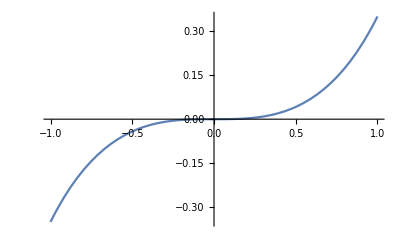

```mathematica
f=NDSolve[{y'[x]==x^2+y[x]^2,y[0]==0},y[x],{x,-1,1}];
a=Plot[Evaluate[y[x]/.f[[1]]],{x,-1,1}]
```

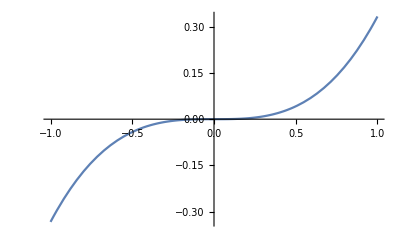

```mathematica
b=Plot[{y=x^3/3},{x,-1,1}]
```

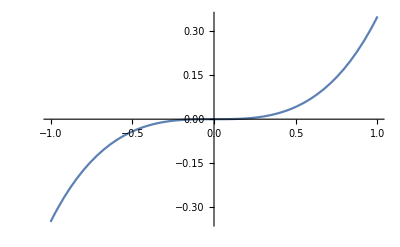

```mathematica
c=Plot[{y=x^7/63+x^3/3},{x,-1,1}]
```

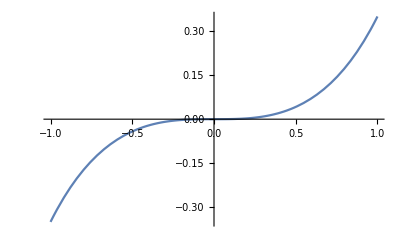

```mathematica
d=Plot[{y=x^15/59535+2x^11/2079+x^7/63+x^3/3},{x,-1,1}]
```

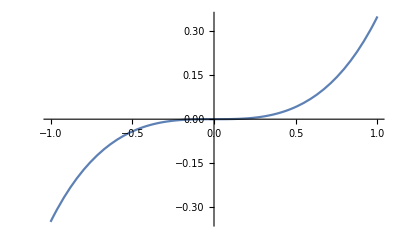

```mathematica
e=Plot[{y=x^3/3+x^7/63+(2 x^11)/2079+(13 x^15)/218295+(82 x^19)/37328445+(662 x^23)/10438212015+(4 x^27)/3341878155+x^31/109876902975},{x,-1,1}]
```

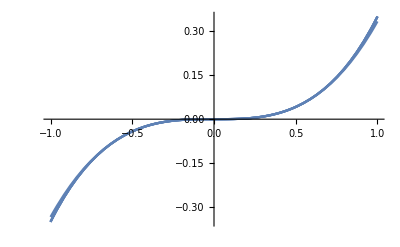

```mathematica
Show[a,b,c,d,e]
```